```mathematica
pts=Import["Desktop/Code/Homework/IndividualProject/Problem2/testcase/square_50/data.txt","Table"]
```

{{1.53451,21.9018},{2.32061,65.2604},{2.48136,97.7068},{4.20522,19.6462},{5.60969,40.0153},{6.88296,20.3503},{7.59369,46.6409},{8.83831,39.3913},{9.75964,42.8617},{11.1494,65.4252},{13.6418,91.7926},{14.3826,90.5611},{16.739,49.9926},{19.526,71.8844},{21.3959,58.1272},{21.6177,70.9476},{22.1118,29.833},{22.619,76.5514},{23.2124,33.6068},{27.11,14.3947},{29.756,81.5793},{32.4109,91.4532},{37.3877,51.4489},{39.2137,64.3009},{40.4255,87.2923},{40.9676,30.0681},{42.019,90.6447},{44.5968,98.9416},{45.4823,20.4589},{46.2021,26.2397},{48.4333,66.7778},{51.1568,1.80288},{52.071,10.6039},{52.577,57.3386},{55.0325,39.1332},{55.2465,16.2644},{60.5101,61.2304},{61.8112,70.9151},{63.7004,69.4317},{65.7023,41.0867},{67.6261,35.1143},{70.0793,41.3429},{75.6591,53.6341},{75.9241,82.3535},{80.4459,75.9431},{80.7844,66.2578},{88.7432,62.8761},{93.0826,0.535265},{93.5544,90.3978},{98.5264,32.8995}}

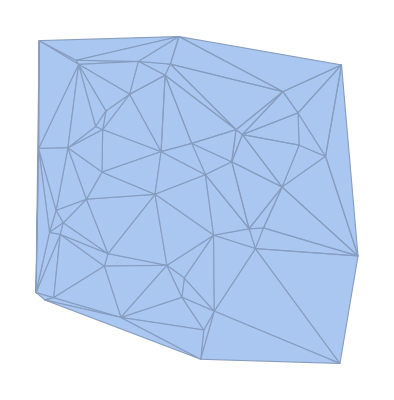

```mathematica
R=DelaunayMesh[pts]
```

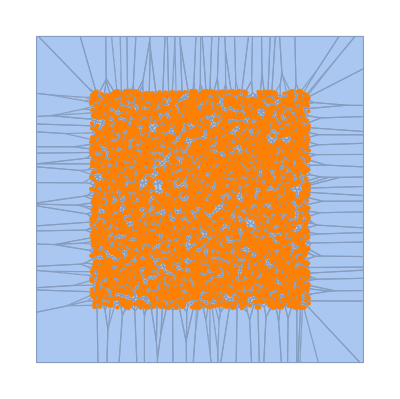

```mathematica
Show[%,Graphics[{Orange,Point[pts]}]]
```